## Елисеев С. Г.

## Лабораторная работа №5 : Численные расчёты в системе Mathematica

## 5.1

#### 5.1.а | Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

#### 5.1.б | Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3   5
```

15

```mathematica
2+         7
```

9

#### 5.1.в | Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

#### 5.1.г | Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
3 /7.
```

0.428571

```mathematica
17.^(1/2)
```

4.12311

#### 5.1.д | Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
5     (4-1)
```

15

## 5.2

#### 5.2.а | С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

#### 5.2.б | Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]),40]
```

7.499274028×10^-13

#### 5.2.в | Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

#### 5.2.г | Последовательно введите выражения | Справедливо ли неравенство

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## 5.3

#### 5.3.а | Решить уравнения

```mathematica
NSolve[Sqrt[x+2]+4*x==4,x] (*Nsolve - ф., которая используется для решения системы уравнений, у неё есть два аргумента, первый - уравнение или списко уравнений, а второй - переменная или список мён, относительно которых нужно разрешить уравнение*)
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

#### 5.3.б | Решить системы уравнений

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

#### 5.3.в | Придумать уравнение или систему уравнений и найдите её численное решение

```mathematica
NSolve[{x^3+y^3+2*x^2*y+2*y^2*x==64,2*x+y==4}, {x,y},Reals]
```

{{x→0.,y→4.}}

## 5.4

#### Вариант 8| 8cox(x)=x на отрезке x=>{-2,6}

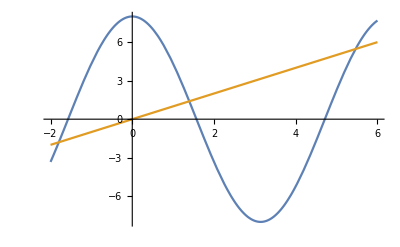

```mathematica
Plot[{8*Cos[x], x}, {x, -2,6}]
```

```mathematica
FindRoot[8*Cos[x]==x,{x,-2,6}] (*находит тольок одно численное решение при каждоам обращении к ней, в качестве одного из аргументов указываем число, с которого начинается поиск его точного значения*)
```

{x→5.4643}

## 5.5

#### Вариант 8 | y’’+2y’th(x)+3y=0, y(0)=-1, y’(0)=2 на отрезке x=>{-3,2}

```mathematica
funcy=NDSolve[{y''[x]+2*y'[x]*Tanh[x]+3*y[x]==0,y[0]==-1,y'[0]==2},y,{x,-3,2}]
(*NDSolve - функция, которая используется для численного решения дифференциальных уравнений, имеет три аргумента: 1 - список, который включает дифференциальное уравнение и необходимое число граничных или начальных значений, 2 - имя функции, отн. кот. реш. урав. 3- имя незав. перемен., решение ищется на отрезке от xmin до xmax,
двойной зна кравенств - общее правило записи всех уравнений, все её производные должны быть записаны с аргументом в кв. скобках *)
```

{{y→InterpolatingFunction[…]}}

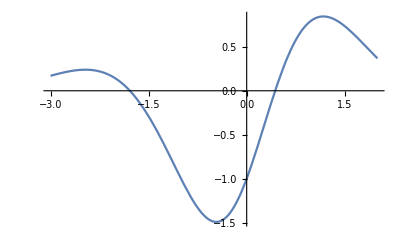

```mathematica
Plot[y[x]/.funcy,{x,-3,2}]
```

#### 5.5.a | Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
r1=FindRoot[y[x]/.funcy,{x,-1.8}]
```

{x→-1.78623}

```mathematica
r2=FindRoot[y[x]/.funcy,{x,0.4}]
```

{x→0.43521}

#### 5.5.б | Найдите значения производной y’(x) в точках, где y(x)=0

```mathematica
D[y[x]/.funcy,x]/.r1
```

{-0.798593}

```mathematica
D[y[x]/.funcy,x]/.r2
```

{2.23451}

#### 5.5.в | Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
LocalMaxim=FindRoot[D[y[x]/.funcy,x]==0,{x,1}](*Производная равна 0 в точках, где касательная к графику функции паралельна оси абсцисс(точки экстремума)*)
```

{x→1.17248}

```mathematica
y[x]/.funcy/.LocalMaxim
```

{0.845325}

#### 5.5.г | С помощью функции FindMaximum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте ‘в’

```mathematica
FindMaximum[y[x]/.funcy,{x,1}]
```

{0.845325,{x→1.17248}}

## 5.6

#### 5.6.а | Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях: y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x). Используя функцию Table, определите список численных данных, каждый элемент которого содержит два элемента (x,y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Дy

#### 1)

```mathematica
firstData=Table[{x,(8+14*x+2*x^2+6*x^3+2*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
(*0 <= x <=5, 0.2 - шаг*)
```

{{0.,7.92498},{0.2,11.7094},{0.4,15.2278},{0.6,19.6009},{0.8,23.2519},{1.,32.1001},{1.2,44.455},{1.4,60.6419},{1.6,70.48},{1.8,93.4194},{2.,123.654},{2.2,145.738},{2.4,212.729},{2.6,279.677},{2.8,311.168},{3.,370.599},{3.2,438.939},{3.4,622.666},{3.6,752.952},{3.8,864.713},{4.,1031.6},{4.2,1253.53},{4.4,1362.98},{4.6,1660.23},{4.8,1752.88},{5.,1917.67}}

#### 2)

```mathematica
secondData=Table[{x,(13+28*x+42*Sin[x]+5*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,18.6261},{0.2,34.7688},{0.4,49.4611},{0.6,57.5282},{0.8,74.6181},{1.,71.334},{1.2,90.3962},{1.4,87.028},{1.6,98.0437},{1.8,112.156},{2.,113.675},{2.2,97.5636},{2.4,94.8173},{2.6,107.472},{2.8,107.436},{3.,93.4262},{3.2,88.3687},{3.4,84.0933},{3.6,84.0489},{3.8,88.0596},{4.,92.9229},{4.2,88.4674},{4.4,101.994},{4.6,97.5177},{4.8,116.42},{5.,111.241}}

#### 5.6.б | Изобразите полученные точки на координатной плоскости

```mathematica
1)
```

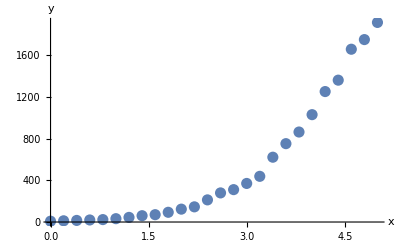

```mathematica
y1=ListPlot[firstData,PlotStyle->PointSize[0.02], AxesLabel->{"x","y"}]
```

```mathematica
2)
```

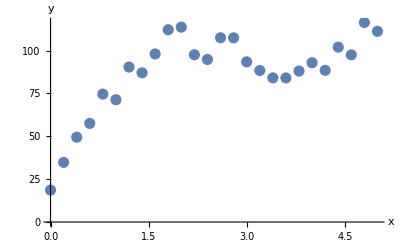

```mathematica
p1=ListPlot[secondData,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

#### 5.6.в | С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
1)
```

```mathematica
apr1=Fit[firstData,{1,x,x^2,x^3,x^4},x] (*первый аргумент списко данных, второй - список ф., третий - имя независимой переменной*)
```

-16.3584+177.751 x-189.141 x^2+77.5424 x^3-6.20202 x^4

```mathematica
apr2=Fit[firstData,{1,x,Sin[x]},x](*экспериментальные точки*)
```

63.6708+202.03 x-422.899 Sin[x]

```mathematica
2)
```

```mathematica
aproc1=Fit[secondData,{1,x,Sin[x],Cos[x]},x]
```

10.3747+29.1617 x+8.75182 Cos[x]+42.8547 Sin[x]

```mathematica
aproc2=Fit[secondData,{1,x,x^2,x^3},x](*экспериментальные точки*)
```

13.6592+103.847 x-38.9043 x^2+4.44281 x^3

#### 5.6.г | На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
1)
```

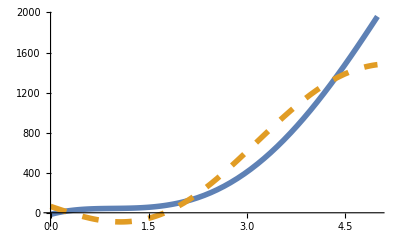

```mathematica
y2=Plot[{apr1,apr2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
Show[y1,y2]
```

-Graphics-

```mathematica
2)
```

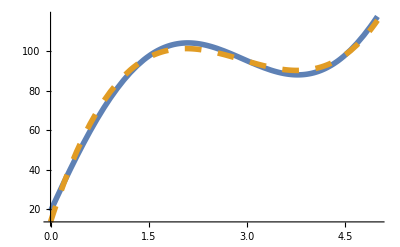

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
Show[p1,p2]
```

-Graphics-